```mathematica
ClearAll["Global`*"];
```

```mathematica
HSk[kx_]:=(t1+t2 Cos[kx])PauliMatrix[1]+t2 Sin[kx]PauliMatrix[2]+(-μ +λ Sin[kx])PauliMatrix[3]-I γ IdentityMatrix[2];
```

```mathematica
HBx[kx_]:=tx(1+Cos[kx])PauliMatrix[1]+tx  Sin[kx]PauliMatrix[2]+(-μ2-I γ )IdentityMatrix[2];HBk[kx_,ky_]:=HBx[kx]+2ty Cos[ky]IdentityMatrix[2];
```

```mathematica
T0[kx_]:=HBx[kx]
T1[kx_]:=ty IdentityMatrix[2]
Tm1[kx_]:=ty IdentityMatrix[2]
HBr[kx_,Ly_]:=Normal[ArrayFlatten[TensorProduct[SparseArray[Band[{1,2},{Ly,Ly}]->1,{Ly,Ly}],T1[kx]]+TensorProduct[SparseArray[Band[{2,1},{Ly,Ly}]->1,{Ly,Ly}],Tm1[kx]]+TensorProduct[SparseArray[Band[{1,1},{Ly,Ly}]->1,{Ly,Ly}],T0[kx]]]];
SelfEne[omega_,kx_,ny_]:={{t3^2*Inverse[omega IdentityMatrix[ny*2]-HBr[kx,ny]][[1,1]],0},{0,0}};
```

```mathematica
GSk[omega_,kx_,ny_]:=Inverse[omega IdentityMatrix[2]-HSk[kx]-SelfEne[omega,kx,ny]];
```

```mathematica
tx=1;ty=3.5;μ2=0.3;γ =0.1;ny=300;
t3=0.6;
```

```mathematica
t1=1.2;t2=-1;μ=0.2;λ=-1;
ESk1[kx_]:=Sqrt[(t1+t2 Cos[kx])^2+(t2 Sin[kx])^2+(-μ +λ Sin[kx])^2];
ESk2[kx_]:=-Sqrt[(t1+t2 Cos[kx])^2+(t2 Sin[kx])^2+(-μ +λ Sin[kx])^2];
```

```mathematica
GSkapp[omega_,kx_,ny_]:=Inverse[omega IdentityMatrix[2]-HSk[kx]-SelfEne[0,0,ny]];
```

```mathematica
SE2[kx_]:=SelfEne[5,kx,ny];
EV1=Flatten[Table[Eigenvalues[HSk[kx]+SE2[kx]],{kx,-Pi,Pi,2Pi/80}]];
```

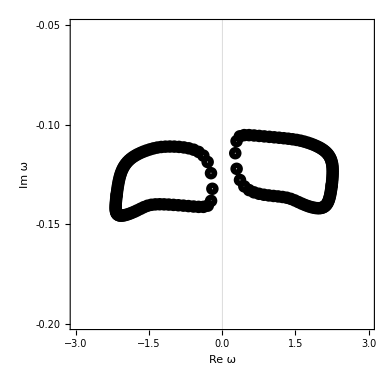

```mathematica
A3a=ListPlot[ReIm[EV1],PlotTheme->"Scientific",PlotMarkers->{Graphics/@{Circle[{0,0},1]},0.02},PlotStyle->{Black,Thickness[0.15]},PlotRange->{{-3,3},{-0.2,-0.05}},LabelStyle->{FontFamily->"Times New Roman",25,GrayLevel[0]},BaseStyle->{FontFamily->"Times New Roman",25},FrameLabel->{{"Im ω",None},{"Re ω",None}},FrameTicks->{{{{-0.20,"-0.20"},-0.15,{-0.10,"-0.10"},-0.05},Automatic},{Automatic,Automatic}},AspectRatio->1,ImageSize->390]
```

```mathematica
cAkapp=-Im[Sum[1/(w1+I w2-EV1[[i]]),{i,1,Length[EV1]}]]/(Pi*Length[EV1]/2);
```

```mathematica
Col1[x_]:=If[x>0,RGBColor[1,0,0,(x/5)^1],RGBColor[0,0,1,(-x/5)^1]];
```

```mathematica
CK1=ParallelTable[cAkapp,{w2,-0.2,-0.05,0.15/1000},{w1,-3,3,6/1000}];
```

```mathematica
A3b=ListDensityPlot[CK1,ColorFunction->Col1,ColorFunctionScaling->False,PlotRange->{-10,10},DataRange->{{-3,3},{-0.2,-0.05}},PlotTheme->"Scientific",AspectRatio->1,LabelStyle->{FontFamily->"Times New Roman",25,GrayLevel[0]},BaseStyle->{FontFamily->"Times New Roman",25},FrameLabel->{{"Im ω",None},{"Re ω",None}},ImageSize->390]
```

```mathematica
Show[{A3a,A3b}]
```